# Projekt 2 - Normal Distribution

## KTH/ICT:IX1501 - Statistics

Joe Huldén, joeda@kth.se
Gustav Wiiala, wiiala@kth.se

KTH/ICT - Communication Systems

2015-12-03

## Det relativa felet av Normal Approximation

### Projekt 2

#### Uppgift 1: Study of the average t̄=1/n ∑_(k=1)^n t_k of n=20 interarrival times.

Plot the absolute error of the pdf_(t̄)(t) and the cdf_(t̄)(t) using the normal approximation. Make also a plot of the relative error of P(t̄>x), μ-2σ/√n<x<μ+2σ/√n

20/3

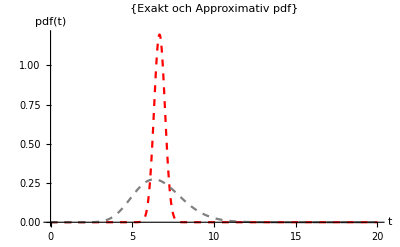

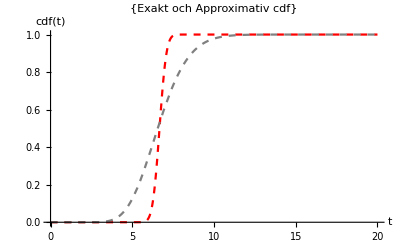

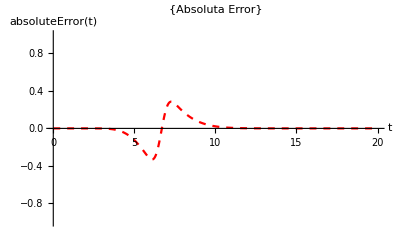

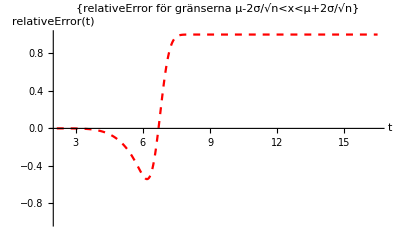

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
λ = 1/3; (*förväntade tidsintervall*)
n = 20; (*antalet iid rvs*)

gamma =ErlangDistribution[n, 1/λ];
Subscript[μ, exakt]  = Mean[gamma]
σ = StandardDeviation[gamma];

(*Approximativa distro*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ/ √n];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[gamma,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;


relativeError[x_] := absoluteError[x]/Pexact[x]






(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
Plot[{PDF[approxi,t],PDF[gamma,t]},{t,0,20},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt och Approximativ pdf"},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange-> Full]

(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
Plot[{CDF[approxi,t],CDF[gamma,t]},{t,0,20},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt och Approximativ cdf"},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}]
(*Plot av Absolut fel*)
Plot[{absoluteError[t]},{t,0,20},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[t],HoldForm[absoluteError[t]]}]

(*
Plot[{relativeError[t]},{t,0,100},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Relativt Error"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
*)


Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```

```mathematica
wi
```

wi

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

#### Uppgift 2:Study the number of incoming calls during one hour

TASK2: Plot the absolute and relative error of the probability function using normal approximation. Conclusion?

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
λ = 1/3; (*förväntade tidsintervall*)
n = 20; (*antalet iid rvs*)

gamma =ErlangDistribution[n, 1/λ];
Subscript[μ, exakt]  = Mean[gamma]
σ = StandardDeviation[gamma];

(*Approximativa distro*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ/ √n];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[gamma,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;


relativeError[x_] := absoluteError[x]/Pexact[x]






(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
Plot[{PDF[approxi,t],PDF[gamma,t]},{t,0,20},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt och Approximativ pdf"},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange-> Full]

(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
Plot[{CDF[approxi,t],CDF[gamma,t]},{t,0,20},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt och Approximativ cdf"},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}]
(*Plot av Absolut fel*)
Plot[{absoluteError[t]},{t,0,20},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[t],HoldForm[absoluteError[t]]}]

(*
Plot[{relativeError[t]},{t,0,100},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Relativt Error"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
*)


Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```

20/3

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
wi
```

wi

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}